```mathematica
DSolve[{y''[x]+y[x]*x^2m^4==0},y[x],x]
```

{{y[x]→C[1] ParabolicCylinderD[-1/2,(-1)^(1/4) √2 m x]+C[2] ParabolicCylinderD[-1/2,(-1)^(3/4) √2 m x]}}

```mathematica
ParabolicCylinderD[-1/2,0]
```

(√π)/(2^(1/4) Gamma[3/4])

```mathematica
ParabolicCylinderD[-1/2,0]
```

```mathematica
D[ParabolicCylinderD[-1/2,x],x]
```

1/2 x ParabolicCylinderD[-1/2,x]-ParabolicCylinderD[1/2,x]

```mathematica
Sol[x_,m_]:=ParabolicCylinderD[-1/2,m(1+I)x]-ParabolicCylinder[-1/2,m(-1+I)x]
```

```mathematica
FullSimplify[D[Sol[x],x]/.{x->1}]
```

ⅈ m (m ParabolicCylinderD[-1/2,(1+ⅈ) m]-(1-ⅈ) (ParabolicCylinderD[1/2,(1+ⅈ) m]+ⅈ ParabolicCylinder^(0,1)[-1/2,(-1+ⅈ) m]))

```mathematica
der[m_]:=ⅈ m (m ParabolicCylinderD[-1/2,(1+ⅈ) m]-(1-ⅈ) (ParabolicCylinderD[1/2,(1+ⅈ) m]+ⅈ Derivative[0,1][ParabolicCylinder][-1/2,(-1+ⅈ) m]))
```

```mathematica
NSolve[der[m]==0,m]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{m→0.}}

```mathematica
FindRoot[der[m]==0,{m,0.1}]
```

FindRoot::nlnum: The function value {(0.`  + 0.1` ⅈ) ((0.11581335375890106`  - 0.0058136541018157` ⅈ) - (1.`  - 1.` ⅈ) ((0.6423699994229543`  + 0.054797137183475245` ⅈ) + (0.`  + 1.` ⅈ) SuperscriptBox[ is not a list of numbers with dimensions {1} at {m} = {0.1`}.

FindRoot[der[m]==0,{m,0.1}]

```mathematica
N[FullSimplify[der[0.1]]]
```

(-0.0581759-0.0581354 ⅈ)+(0.1-0.1 ⅈ) ParabolicCylinder^(0,1)[-0.5,-0.1+0.1 ⅈ]

```mathematica
N[Derivative[0,1][ParabolicCylinder][-0.5,0.1]]
```

ParabolicCylinder^(0,1)[-0.5,0.1]

```mathematica
N[BesselJ[-1/4,1]]
```

0.669385

```mathematica
N[BesselJ[1/4,1]]
```

0.752231

```mathematica
fun1[x_]:=2^{-5/4}*Sqrt[π x]*(BesselJ[-1/4,x^2/4]+BesselJ[1/4,x^2/4])
```

```mathematica
fun2[x_]:=2^{-5/4}*Sqrt[π x]*(BesselJ[-1/4,x^2/4]-BesselJ[1/4,x^2/4])
```

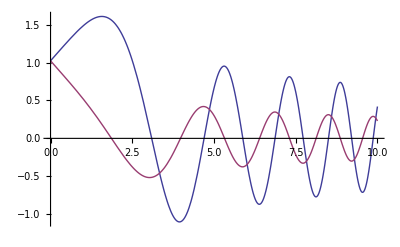

```mathematica
Plot[{fun1[x],fun2[x]},{x,0,10}]
```

```mathematica
funm1[x_]:=1/2 √π √(m x) (BesselJ[-1/4,(m^2 x^2)/2]+BesselJ[1/4,(m^2 x^2)/2])
```

```mathematica
funm2[x_]:=1/2 √π √(m x) (BesselJ[-1/4,(m^2 x^2)/2]-BesselJ[1/4,(m^2 x^2)/2])
```

```mathematica
funderm1=FullSimplify[D[funm1[x],x]]
```

1/2 m √π (m x)^(3/2) (BesselJ[-3/4,(m^2 x^2)/2]-BesselJ[3/4,(m^2 x^2)/2])

```mathematica
funderm2=FullSimplify[D[funm2[x],x]]
```

-1/2 m √π (m x)^(3/2) (BesselJ[-3/4,(m^2 x^2)/2]+BesselJ[3/4,(m^2 x^2)/2])

```mathematica
NSolve[funm1[0]*funderm2[1]-funm2[0]*funderm1[1]==0,m]
```

∞::indet: Indeterminate expression 0 √π ComplexInfinity encountered.

{{}}

```mathematica
Limit[funm1[x],x->0]
```

((m^2)^(3/4) √(π/2))/(m^(3/2) Gamma[3/4])

```mathematica
Limit[funm2[x],x->0]
```

((m^2)^(3/4) √(π/2))/(m^(3/2) Gamma[3/4])

```mathematica
FullSimplify[funderm1/.{x->1}]
```

1/2 m^(5/2) √π (BesselJ[-3/4,m^2/2]-BesselJ[3/4,m^2/2])

```mathematica
FullSimplify[funderm2/.{x->1}]
```

-1/2 m^(5/2) √π (BesselJ[-3/4,m^2/2]+BesselJ[3/4,m^2/2])

```mathematica
FullSimplify[-1/2 m^(5/2) √π (BesselJ[-3/4,m^2/2]+BesselJ[3/4,m^2/2])-1/2 m^(5/2) √π (BesselJ[-3/4,m^2/2]-BesselJ[3/4,m^2/2])==0]
```

m^(5/2) BesselJ[-3/4,m^2/2]==0

```mathematica
BesselJZero[-3/4,10]
```

```mathematica
N[BesselJZero[-3/4,1]]
```

1.05851

```mathematica
Zeros=Table[N[Sqrt[2BesselJZero[-3/4,i]]],{i,1,100}]
```

{1.455,2.92713,3.85758,4.60178,5.24082,5.80979,6.32769,6.80625,7.25326,7.67426,8.07332,8.45355,8.81739,9.1668,9.50336,9.8284,10.143,10.4482,10.7447,11.0332,11.3144,11.5887,11.8567,12.1188,12.3753,12.6266,12.873,13.1148,13.3522,13.5855,13.8148,14.0404,14.2624,14.481,14.6963,14.9086,15.1178,15.3242,15.5279,15.7289,15.9274,16.1234,16.3171,16.5085,16.6977,16.8848,17.0699,17.2529,17.4341,17.6134,17.7908,17.9665,18.1406,18.3129,18.4837,18.6529,18.8205,18.9867,19.1515,19.3148,19.4768,19.6374,19.7968,19.9548,20.1117,20.2673,20.4217,20.5749,20.7271,20.8781,21.028,21.1769,21.3247,21.4715,21.6174,21.7622,21.9061,22.049,22.1911,22.3322,22.4724,22.6118,22.7503,22.888,23.0248,23.1609,23.2961,23.4306,23.5643,23.6972,23.8294,23.9609,24.0917,24.2217,24.3511,24.4797,24.6077,24.7351,24.8618,24.9878}

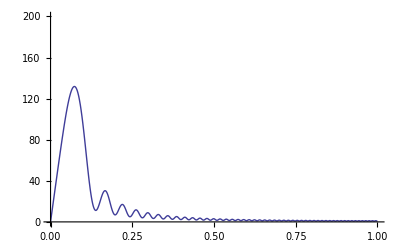

```mathematica
Plot[Sum[(funm1[x]/.{m->Zeros[[i]]})-(funm2[x]/.{m->Zeros[[i]]}),{i,1,100}],{x,0,1},PlotRange->{{0,1},{0,200}}]
```